```mathematica
(* Mathematica*)
allColors=ColorData["Legacy"][[3,1]];
firstCols=Join[{"White","AliceBlue","LightBlue","Cyan","ManganeseBlue","DodgerBlue","Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow","Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow","Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow","Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"},{"White","AliceBlue","LightBlue","Cyan","ManganeseBlue","DodgerBlue","Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow","Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow","Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow","Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"}];
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
```

```mathematica
Clear[f,g,ff,gg,x,ll,kk,mm]
```

```mathematica
f[x_]:=2*x/;0<=x<=1/2
f[x_]:=2-2*x/;1/2<x≤1
```

```mathematica
ff[x_]=f[Mod[Abs[x],1]]
```

f[Mod[Abs[x],1]]

```mathematica
(*second negative cycle tent*)
```

```mathematica
g[x_]:=2*x/;0<=x<=1/2
g[x_]:=-(2-2*x)/;1/2<x≤1
```

```mathematica
gg[x_]=g[Mod[Abs[x],1]]
```

g[Mod[Abs[x],1]]

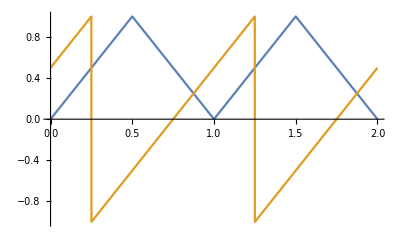

```mathematica
Plot[{ff[x],gg[x+1/4]},{x,0,2}]
```

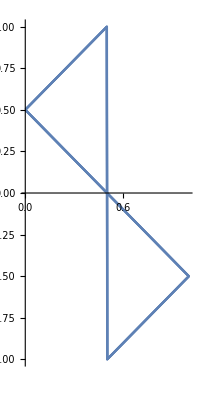

```mathematica
ParametricPlot[{ff[x],gg[x+1/4]},{x,0,4}]
```

```mathematica
Plot[ff[x],{x,0,4}];
```

```mathematica
(* dimension*)
```

```mathematica
s0=N[Log[2]/Log[3]]
```

0.63093

```mathematica
(*scale factor*)
```

```mathematica
sc=3.
```

3.

```mathematica
(*3d functions :2nd function cycled*)
```

```mathematica
kk[x_]=Sum[ff[sc^k*x]/sc^(s0*k),{k,0,20}];
ll[x_]=Sum[gg[sc^k*(x+1/4)]/sc^(s0*k),{k,0,20}];
mm[x_]=Sum[ff[sc^k*(x-1/2)]/sc^(s0*k),{k,0,20}];
```

```mathematica
aa=Flatten[ParallelTable[{i*kk[n/30000],j*ll[n/30000],k*mm[n/30000]},{i,-1,1,2},{j,-1,1,2},{k,-1,1,2},{n,0,30000}],3];
```

```mathematica
Length[aa]
```

240008

```mathematica
g0=ListPointPlot3D[aa,AspectRatio->1,ColorFunction->Hue,ImageSize->2000,PlotRange->All];
```

```mathematica
dlst=ParallelTable[1+Mod[Floor[1+(1+Floor[6*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst]
Max[dlst]
```

8

15

```mathematica
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g2=Graphics3D[{PointSize[.001],ptlst},AspectRatio->1,ImageSize->2000,Axes->False,Background->Black,PlotRange->All];
```

```mathematica
Export["biscuit_Tent_cycle_scale3_phase_triple_sign_color.jpg",{g0,g2}]
(*end*)
```

biscuit_Tent_cycle_scale3_phase_triple_sign_color.jpg